```mathematica
ε=10.^-10;
```

```mathematica
SolveDiff[χ_,f_,ν1_,ν2_,u0_,Δt_,tmax_,Δx_,l_,σ_]:=Module[
{χLeftDiscrete,χRightDiscrete,fDiscrete,ν1Discrete,ν2Discrete,u0Discrete,solve,y,sol},
χLeftDiscrete=Table[χ[x-Δx/2],{x,Δx,l,Δx}];
χRightDiscrete=Table[χ[x+Δx/2],{x,0,l-Δx,Δx}];
fDiscrete=Table[f[x,t+Δt/2],{t,0,tmax,Δt},{x,0,l,Δx}];
ν1Discrete=Table[ν1[t],{t,0,tmax,Δt}];
ν2Discrete=Table[ν2[t],{t,0,tmax,Δt}];
u0Discrete=Table[u0[x],{x,0,l,Δx}];


solve=Table[0,{t,1,tmax/Δt+1},{x,1,l/Δx+1}];
Do[y[t,1]=ν1Discrete[[t]],{t,1,tmax/Δt+1}];
Do[y[t,Floor[l/Δx]+1]=ν2Discrete[[t]],{t,1,tmax/Δt+1}];
Do[y[1,x]=u0Discrete[[x]],{x,1,l/Δx+1}];

LambdaY[t_,x_]:=1/Δx(χRightDiscrete[[x]](y[t,x+1]-y[t,x])/Δx-χLeftDiscrete[[x]](y[t,x]-y[t,x-1])/Δx);

eqs=Flatten[Table[
(y[t+1,x]-y[t,x])/Δt==σ LambdaY[t+1,x]+(1-σ)LambdaY[t,x]+fDiscrete[[t,x]],
{t,1,Floor[tmax/Δt]},
{x,2,Floor[l/Δx]}
]
];
vars = Flatten[
Table[
y[t+1,x],
{t,1,Floor[tmax/Δt]},
{x,2,Floor[l/Δx]}
]
];
sol=Solve[eqs,vars];
Do[solve[[1,x]]=u0Discrete[[x]],{x,1,l/Δx+1}];
Do[solve[[t,1]]=ν1Discrete[[t]],{t,1,tmax/Δt+1}];
Do[solve[[t,Floor[l/Δx]+1]]=ν2Discrete[[t]],{t,1,tmax/Δt+1}];

Do[
(*solve[[t+1,x]]=solve[[t,x]]+Δt(solve[[t,x+1]]-2solve[[t,x]]+solve[[t,x-1]])/Δx^2;*)
solve[[t+1,x]]=First[y[t+1,x]/.sol];

,{t,1,Floor[tmax/Δt]},{x,2,Floor[l/Δx]}
];
Return[solve];
];
```

### Task 1

#### 1.

```mathematica
χ[x_]:=1; f[x_,t_]:=0;
ν1[t_]:=0; ν2[t_]:=0;
u0[x_]:=Sin[π x];
l=1; tmax=1;

Δx=0.1;Δt=1./20; 
Δt/Δx^2
```

5.

#### 2.

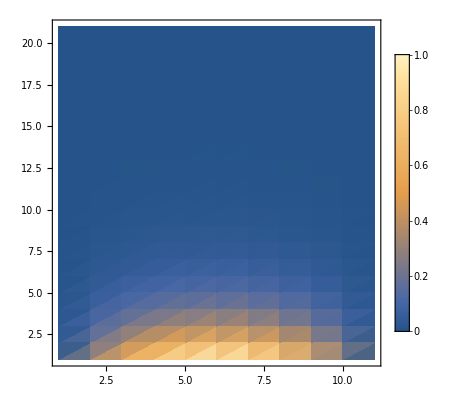

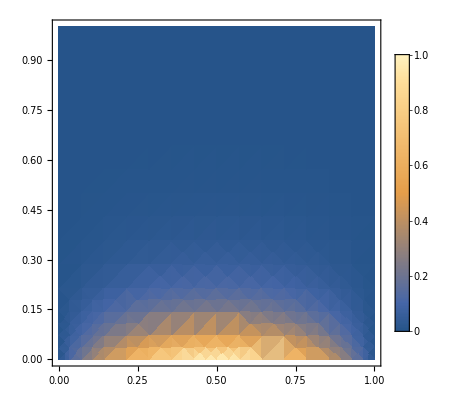

```mathematica
sol[σ_,Δx_]:=SolveDiff[χ,f,ν1,ν2,u0,Δt,tmax,Δx,l,σ];
ListDensityPlot[sol[0.5,0.1],PlotRange->All,PlotLegends->Automatic]
DensityPlot[Exp[-π^2 t]Sin[π x],{x,0,l},{t,0,tmax},PlotRange->All,PlotLegends->Automatic]
```

#### 3.

```mathematica
err=Table[Exp[-π^2 t]Sin[π x],{t,0,tmax,Δt},{x,0,l,Δx}]-sol[0.5,0.1];
Max[Abs[err]]
```

0.00451325

```mathematica
ListPlot3D[Table[Norm[Abs[sol[σ,10^-Δx]-Table[Exp[-π^2 t]Sin[π x],{t,0,tmax,Δt},{x,0,l,10^-Δx}]]],{σ,0,2,0.1},{Δx,1,2} ],AxesLabel->{"Δx","σ","Error"}]
```

-Graphics3D-

### Task 2

5.

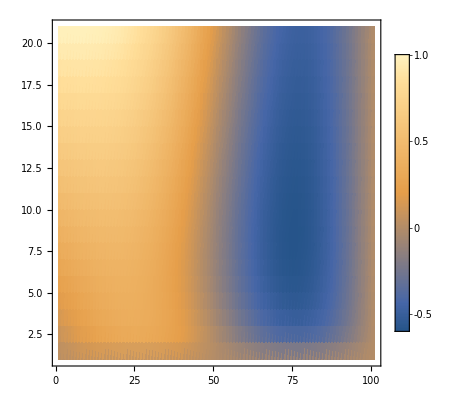

```mathematica
χ[x_]:=Exp[-x]; f[x_,t_]:=10Sin[2π x];
ν1[t_]:=t; ν2[t_]:=0;
u0[x_]:=0;
l=1; tmax=1;

Δx=0.1;Δt=1./20; 
Δt/Δx^2

Show[ListDensityPlot[sol[0.5,0.01],PlotRange->All,PlotLegends->Automatic]]
```